GEOMETRICKÁ TRANSFORMÁCIA DOMČEKA - ZLOŽITÁ ÚLOHA

==========================================

ZADANIE PRE ŠTUDENTA:

Majme domček ABCDE s vrcholmi:

(-3 | -1
-3 | 2
0 | 4
3 | 2
3 | -1)

Vykonajte postupne tieto transformácie:

1. Vykonajte symetriu domčeka v 2D priestore podľa priamky y = x

2. Vykonajte skosenie domčeka v 2D priestore v smere osi x s koeficientom 3/2

3. Vykonajte zväčšenie v smere osi x s koeficientom 2 a zväčšenie v smere osi y s koeficientom 3/2 domčeka

RIEŠENIE:

GEOMETRICKÁ TRANSFORMÁCIA DOMČEKA - ZLOŽITÁ ÚLOHA

==========================================

POČIATOČNÝ DOMČEK:

Vrcholy domčeka ABCDE:

(-3 | -1
-3 | 2
0 | 4
3 | 2
3 | -1)

Vlastnosti domčeka:

Obsah: 6

Obvod: 19

PRVÁ TRANSFORMÁCIA: Symetria

GEOMETRICKÉ TRANSFORMÁCIE DOMČEKA - SYMETRIA

========================================

ZADANIE:

Majme domček ABCDE s vrcholmi:

(-3 | -1
-3 | 2
0 | 4
3 | 2
3 | -1)

Vykonajte symetriu v 2D priestore podľa priamky x - y = 0.

TEÓRIA MATICOVÉHO ZOBRAZENIA SYMETRIE:

Pri symetrii podľa priamky ax + by + c = 0 v 2D priestore môžeme použiť homogénnu transformačnú maticu 3×3:

Homogénna transformačná matica pre symetriu má tvar:

((b^2 - a^2)/(a^2 + b^2) | -2ab/(a^2 + b^2) | -2ac/(a^2 + b^2)
-2ab/(a^2 + b^2) | (a^2 - b^2)/(a^2 + b^2) | -2bc/(a^2 + b^2)
0 | 0 | 1)

Výhoda použitia homogénnej matice je, že zahŕňa lineárnu transformáciu aj posun v jednej matici, čo umožňuje

jednoduché reťazenie viacerých transformácií pomocou násobenia matíc.

VÝPOČET TRANSFORMAČNEJ MATICE PRE SYMETRIU:

Pre našu priamku 1x + -1y + 0 = 0:

Vypočítame jednotlivé prvky matice použitím vzorca:

Menovateľ: a.b2 + b.b2 = 1.b2 + -1.b2 = 2

Prvý riadok matice:

M[1,1] = (b.b2 - a.b2)/(a.b2 + b.b2) = (1 - 1)/(2) = 0

M[1,2] = -2ab/(a.b2 + b.b2) = -2·1·-1/(2) = 1

M[1,3] = -2ac/(a.b2 + b.b2) = -2·1·0/(2) = 0

Druhý riadok matice:

M[2,1] = -2ab/(a.b2 + b.b2) = -2·1·-1/(2) = 1

M[2,2] = (a.b2 - b.b2)/(a.b2 + b.b2) = (1 - 1)/(2) = 0

M[2,3] = -2bc/(a.b2 + b.b2) = -2·-1·0/(2) = 0

Tretí riadok matice:

M[3,1] = 0, M[3,2] = 0, M[3,3] = 1 (štandardné hodnoty pre homogénnu transformáciu)

VÝSLEDNÁ TRANSFORMAČNÁ MATICA:

(0 | 1 | 0
1 | 0 | 0
0 | 0 | 1)

Pre našu priamku x - y = 0:

a = 1

b = -1

c = 0

VÝPOČET SYMETRIE JEDNOTLIVÝCH VRCHOLOV:

VRCHOL A:

Pôvodné súradnice: [-3, -1]

Výpočet pomocou homogénnej matice:

(0 | 1 | 0
1 | 0 | 0
0 | 0 | 1) |  ·  | (-3
-1
1) |  =  | (-1
-3
1)

Podrobný výpočet súradníc:

• Výpočet novej x-ovej súradnice:

= (0 · -3) + (1 · -1) + (0 · 1)

= 0 + -1 + 0

= -1

• Výpočet novej y-ovej súradnice:

= (1 · -3) + (0 · -1) + (0 · 1)

= -3 + 0 + 0

= -3

Výsledná reprezentácia bodu A':

[-1, -3]

--------------------------------------------------

VRCHOL B:

Pôvodné súradnice: [-3, 2]

Výpočet pomocou homogénnej matice:

(0 | 1 | 0
1 | 0 | 0
0 | 0 | 1) |  ·  | (-3
2
1) |  =  | (2
-3
1)

Podrobný výpočet súradníc:

• Výpočet novej x-ovej súradnice:

= (0 · -3) + (1 · 2) + (0 · 1)

= 0 + 2 + 0

= 2

• Výpočet novej y-ovej súradnice:

= (1 · -3) + (0 · 2) + (0 · 1)

= -3 + 0 + 0

= -3

Výsledná reprezentácia bodu B':

[2, -3]

--------------------------------------------------

VRCHOL C:

Pôvodné súradnice: [0, 4]

Výpočet pomocou homogénnej matice:

(0 | 1 | 0
1 | 0 | 0
0 | 0 | 1) |  ·  | (0
4
1) |  =  | (4
0
1)

Podrobný výpočet súradníc:

• Výpočet novej x-ovej súradnice:

= (0 · 0) + (1 · 4) + (0 · 1)

= 0 + 4 + 0

= 4

• Výpočet novej y-ovej súradnice:

= (1 · 0) + (0 · 4) + (0 · 1)

= 0 + 0 + 0

= 0

Výsledná reprezentácia bodu C':

[4, 0]

--------------------------------------------------

VRCHOL D:

Pôvodné súradnice: [3, 2]

Výpočet pomocou homogénnej matice:

(0 | 1 | 0
1 | 0 | 0
0 | 0 | 1) |  ·  | (3
2
1) |  =  | (2
3
1)

Podrobný výpočet súradníc:

• Výpočet novej x-ovej súradnice:

= (0 · 3) + (1 · 2) + (0 · 1)

= 0 + 2 + 0

= 2

• Výpočet novej y-ovej súradnice:

= (1 · 3) + (0 · 2) + (0 · 1)

= 3 + 0 + 0

= 3

Výsledná reprezentácia bodu D':

[2, 3]

--------------------------------------------------

VRCHOL E:

Pôvodné súradnice: [3, -1]

Výpočet pomocou homogénnej matice:

(0 | 1 | 0
1 | 0 | 0
0 | 0 | 1) |  ·  | (3
-1
1) |  =  | (-1
3
1)

Podrobný výpočet súradníc:

• Výpočet novej x-ovej súradnice:

= (0 · 3) + (1 · -1) + (0 · 1)

= 0 + -1 + 0

= -1

• Výpočet novej y-ovej súradnice:

= (1 · 3) + (0 · -1) + (0 · 1)

= 3 + 0 + 0

= 3

Výsledná reprezentácia bodu E':

[-1, 3]

--------------------------------------------------

ŠPECIÁLNE MATICE PRE NIEKTORÉ TYPY SYMETRIÍ:

Pre priamku y = x je homogénna transformačná matica:

(0 | 1 | 0
1 | 0 | 0
0 | 0 | 1)

POSTUP:

Pre výpočet osovej symetrie podľa priamky x - y = 0 používame vzorce:

Všeobecný vzorec pre výpočet symetrie bodu [x, y] podľa priamky ax + by + c = 0:

x' = x - 2a(ax + by + c)/(a.b2 + b.b2)

y' = y - 2b(ax + by + c)/(a.b2 + b.b2)

Tento vzorec môžeme zapísať v maticovej forme pomocou homogénnych súradníc [x, y, 1]

ako násobenie s 3×3 maticou, čo umožňuje jednoduché zreťazenie transformácií.

Naše hodnoty koeficientov:

a = 1

b = -1

c = 0

Rovnica osi symetrie: x - y = 0

Normálový vektor osi symetrie: (1, -1)

VÝSLEDOK TRANSFORMÁCIE CELÉHO DOMČEKA:

Pôvodný domček ABCDE:

(-3 | -1
-3 | 2
0 | 4
3 | 2
3 | -1)

Domček po symetrii A'B'C'D'E':

(-1 | -3
2 | -3
4 | 0
2 | 3
-1 | 3)

VIZUALIZÁCIA TRANSFORMÁCIE:

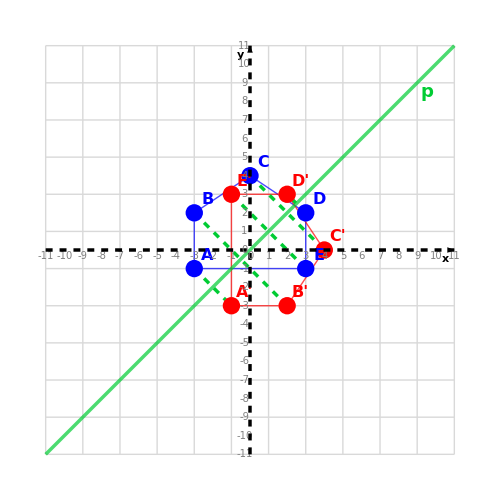

LEGENDA:

• Modré body a čiary: Pôvodný domček

• Červené body a čiary: Domček po symetrii

• Zelené čiara: Os symetrie

• Zelené prerušované čiary: Spojenia zodpovedajúcich si vrcholov

• Červená: Transformačná matica

• Modrá: Vstupné súradnice

• Fialová: Medzivýpočty

• Zelená: Výsledné súradnice

Pôvodné vrcholy (modrá):

Vrchol A: {-3,-1}

Vrchol B: {-3,2}

Vrchol C: {0,4}

Vrchol D: {3,2}

Vrchol E: {3,-1}

Výsledné vrcholy (červená):

Vrchol A': {-1,-3}

Vrchol B': {2,-3}

Vrchol C': {4,0}

Vrchol D': {2,3}

Vrchol E': {-1,3}

MATEMATICKÉ VLASTNOSTI:

• Symetria podľa priamky je izometrická transformácia - zachováva vzdialenosti medzi bodmi

• Symetria zachováva veľkosť a tvar geometrických útvarov

• Symetria zachováva uhly medzi úsečkami a ich dĺžky

• Symetria zachováva obsahy a obvody

• Body ležiace na osi symetrie zostávajú po symetrii nezmenené

• Aplikovaním symetrie dvakrát získame pôvodný obraz - je to transformácia rádu 2

• Spojnica bodu a jeho obrazu je vždy kolmá na os symetrie

• Stred spojnice bodu a jeho obrazu vždy leží na osi symetrie

VÝZNAMNÉ OSI SYMETRIE:

• Os x (y = 0): bod [x, y] sa zobrazí na [x, -y]

• Os y (x = 0): bod [x, y] sa zobrazí na [-x, y]

• Priamka y = x: bod [x, y] sa zobrazí na [y, x]

• Priamka y = -x: bod [x, y] sa zobrazí na [-y, -x]

DRUHÁ TRANSFORMÁCIA: Skosenie

GEOMETRICKÉ TRANSFORMÁCIE DOMČEKA - SKOSENIE

========================================

ZADANIE:

Majme domček ABCDE s vrcholmi:

(-1 | -3
2 | -3
4 | 0
2 | 3
-1 | 3)

Vykonajte skosenie domčeka v 2D priestore v smere osi x s koeficientom k = 3/2.

Transformačná matica skosenia:

(1 | 3/2
0 | 1)

POSTUP:

Pre výpočet použijeme maticu skosenia:

Transformačná matica pre skosenie v smere osi x:

(1 | k
0 | 1)

Vzorec pre výpočet nových súradníc pri skosení v smere osi x:

x' = x + k·y

y' = y

Naša hodnota k = 3/2

TEÓRIA MATICOVÉHO ZOBRAZENIA SKOSENIA:

Pri skosení v 2D priestore používame transformačné matice, ktoré umožňujú vyjadriť skosenie ako maticové násobenie:

Obecná transformačná matica skosenia:

(1 | k
0 | 1)

Ak je bod P = [x, y] v 2D priestore, skosenie môžeme zapísať ako maticové násobenie:

(1 | k
0 | 1) · (x
y) = (x + k·y
y)

Pre naše hodnoty skosenia:

k = 3/2 (koeficient skosenia v smere osi x)

VÝPOČET SKOSENIA JEDNOTLIVÝCH VRCHOLOV:

VRCHOL A:

Pôvodné súradnice: [-1, -3]

Maticový zápis transformácie bodu A:

(1 | 3/2
0 | 1) |  ·  | (-1
-3) |  =  | (-11/2
-3)

Podrobný výpočet jednotlivých súradníc:

• Výpočet novej x-ovej súradnice (1. riadok matice):

[ | 1 | 3/2 | ] · [ | -1 | -3 | ]^T = | -11/2

= (1 · -1) + (3/2 · -3)

= (1 · -1) + (3/2 · -3)

= -1 + -9/2

= -11/2

• Výpočet novej y-ovej súradnice (2. riadok matice):

[ | 0 | 1 | ] · [ | -1 | -3 | ]^T = | -3

= (0 · -1) + (1 · -3)

= (0 · -1) + (1 · -3)

= 0 + -3

= -3

Pre skosenie v smere osi x:

- X-ová súradnica sa mení podľa hodnoty Y: x' = x + k·y

- Y-ová súradnica zostáva nezmenená: y' = y

Výsledné súradnice bodu A' = [-11/2, -3]

Alternatívny výpočet pomocou základných vzorcov skosenia:

x' = x + k·y  =>  -1 + 3/2·-3 = -11/2

y' = y  =>  -3 = -3

Výsledné súradnice vrcholu A':

[-11/2, -3]

--------------------------------------------------

VRCHOL B:

Pôvodné súradnice: [2, -3]

Maticový zápis transformácie bodu B:

(1 | 3/2
0 | 1) |  ·  | (2
-3) |  =  | (-5/2
-3)

Podrobný výpočet jednotlivých súradníc:

• Výpočet novej x-ovej súradnice (1. riadok matice):

[ | 1 | 3/2 | ] · [ | 2 | -3 | ]^T = | -5/2

= (1 · 2) + (3/2 · -3)

= (1 · 2) + (3/2 · -3)

= 2 + -9/2

= -5/2

• Výpočet novej y-ovej súradnice (2. riadok matice):

[ | 0 | 1 | ] · [ | 2 | -3 | ]^T = | -3

= (0 · 2) + (1 · -3)

= (0 · 2) + (1 · -3)

= 0 + -3

= -3

Pre skosenie v smere osi x:

- X-ová súradnica sa mení podľa hodnoty Y: x' = x + k·y

- Y-ová súradnica zostáva nezmenená: y' = y

Výsledné súradnice bodu B' = [-5/2, -3]

Alternatívny výpočet pomocou základných vzorcov skosenia:

x' = x + k·y  =>  2 + 3/2·-3 = -5/2

y' = y  =>  -3 = -3

Výsledné súradnice vrcholu B':

[-5/2, -3]

--------------------------------------------------

VRCHOL C:

Pôvodné súradnice: [4, 0]

Maticový zápis transformácie bodu C:

(1 | 3/2
0 | 1) |  ·  | (4
0) |  =  | (4
0)

Podrobný výpočet jednotlivých súradníc:

• Výpočet novej x-ovej súradnice (1. riadok matice):

[ | 1 | 3/2 | ] · [ | 4 | 0 | ]^T = | 4

= (1 · 4) + (3/2 · 0)

= (1 · 4) + (3/2 · 0)

= 4 + 0

= 4

• Výpočet novej y-ovej súradnice (2. riadok matice):

[ | 0 | 1 | ] · [ | 4 | 0 | ]^T = | 0

= (0 · 4) + (1 · 0)

= (0 · 4) + (1 · 0)

= 0 + 0

= 0

Pre skosenie v smere osi x:

- X-ová súradnica sa mení podľa hodnoty Y: x' = x + k·y

- Y-ová súradnica zostáva nezmenená: y' = y

Výsledné súradnice bodu C' = [4, 0]

Alternatívny výpočet pomocou základných vzorcov skosenia:

x' = x + k·y  =>  4 + 3/2·0 = 4

y' = y  =>  0 = 0

Výsledné súradnice vrcholu C':

[4, 0]

--------------------------------------------------

VRCHOL D:

Pôvodné súradnice: [2, 3]

Maticový zápis transformácie bodu D:

(1 | 3/2
0 | 1) |  ·  | (2
3) |  =  | (13/2
3)

Podrobný výpočet jednotlivých súradníc:

• Výpočet novej x-ovej súradnice (1. riadok matice):

[ | 1 | 3/2 | ] · [ | 2 | 3 | ]^T = | 13/2

= (1 · 2) + (3/2 · 3)

= (1 · 2) + (3/2 · 3)

= 2 + 9/2

= 13/2

• Výpočet novej y-ovej súradnice (2. riadok matice):

[ | 0 | 1 | ] · [ | 2 | 3 | ]^T = | 3

= (0 · 2) + (1 · 3)

= (0 · 2) + (1 · 3)

= 0 + 3

= 3

Pre skosenie v smere osi x:

- X-ová súradnica sa mení podľa hodnoty Y: x' = x + k·y

- Y-ová súradnica zostáva nezmenená: y' = y

Výsledné súradnice bodu D' = [13/2, 3]

Alternatívny výpočet pomocou základných vzorcov skosenia:

x' = x + k·y  =>  2 + 3/2·3 = 13/2

y' = y  =>  3 = 3

Výsledné súradnice vrcholu D':

[13/2, 3]

--------------------------------------------------

VRCHOL E:

Pôvodné súradnice: [-1, 3]

Maticový zápis transformácie bodu E:

(1 | 3/2
0 | 1) |  ·  | (-1
3) |  =  | (7/2
3)

Podrobný výpočet jednotlivých súradníc:

• Výpočet novej x-ovej súradnice (1. riadok matice):

[ | 1 | 3/2 | ] · [ | -1 | 3 | ]^T = | 7/2

= (1 · -1) + (3/2 · 3)

= (1 · -1) + (3/2 · 3)

= -1 + 9/2

= 7/2

• Výpočet novej y-ovej súradnice (2. riadok matice):

[ | 0 | 1 | ] · [ | -1 | 3 | ]^T = | 3

= (0 · -1) + (1 · 3)

= (0 · -1) + (1 · 3)

= 0 + 3

= 3

Pre skosenie v smere osi x:

- X-ová súradnica sa mení podľa hodnoty Y: x' = x + k·y

- Y-ová súradnica zostáva nezmenená: y' = y

Výsledné súradnice bodu E' = [7/2, 3]

Alternatívny výpočet pomocou základných vzorcov skosenia:

x' = x + k·y  =>  -1 + 3/2·3 = 7/2

y' = y  =>  3 = 3

Výsledné súradnice vrcholu E':

[7/2, 3]

--------------------------------------------------

VÝSLEDOK TRANSFORMÁCIE CELÉHO DOMČEKA:

Pôvodný domček ABCDE:

(-1 | -3
2 | -3
4 | 0
2 | 3
-1 | 3)

Skosený domček A'B'C'D'E':

(-11/2 | -3
-5/2 | -3
4 | 0
13/2 | 3
7/2 | 3)

VIZUALIZÁCIA TRANSFORMÁCIE:

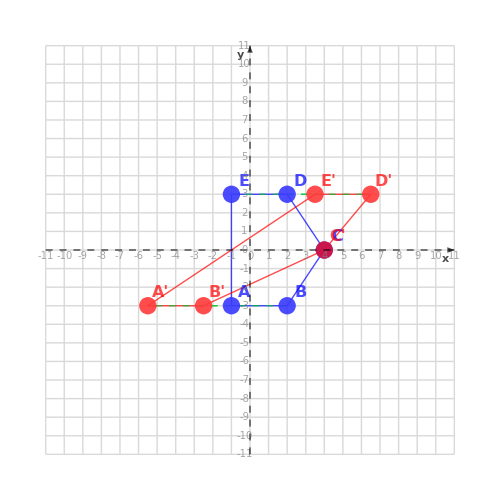

LEGENDA:

• Modré body a čiary: Pôvodný domček

• Červené body a čiary: Skosený domček

• Zelené prerušované čiary: Dráha pohybu vrcholov pri skosení

FAREBNÉ OZNAČENIA V MATICOVÝCH VÝPOČTOCH:

• Červená: Transformačná matica

• Modrá: Vstupné súradnice

• Fialová: Medzivýpočty

• Zelená: Výsledné súradnice

Pôvodné vrcholy (modrá):

Vrchol A: {-1,-3}

Vrchol B: {2,-3}

Vrchol C: {4,0}

Vrchol D: {2,3}

Vrchol E: {-1,3}

Výsledné vrcholy (červená):

Vrchol A': {-11/2,-3}

Vrchol B': {-5/2,-3}

Vrchol C': {4,0}

Vrchol D': {13/2,3}

Vrchol E': {7/2,3}

Inverzná transformácia:

Pre vrátenie do pôvodného stavu použite koeficient skosenia:

k' = -k = -3/2 v smere osi x

MATEMATICKÉ VLASTNOSTI:

• Skosenie je lineárna transformácia, ktorá zachováva rovnobežnosť priamok s jednou z osí

• Pri skosení v smere osi x zostávajú zachované y-ové súradnice všetkých bodov

• Zvislé priamky (rovnobežné s osou y) zostávajú zvislé

• Skosenie mení uhly a tvary geometrických útvarov, ale zachováva ich obsah

• Body ležiace na osi, ktorá je rovnobežná so smerom skosenia, sa nemenia

• Skosenie je afínna transformácia, ktorá nezachováva vzdialenosti ani uhly

ŠPECIÁLNE PRÍPADY:

• Pre k = 0 je skosenie identickou transformáciou (bod sa nemení)

• Pre veľké hodnoty |k| sa útvar výrazne skosí a môže byť ťažšie rozpoznateľný

• Pre k = 1 sa vytvorí rovnoramenný pravouhlý trojuholník z pôvodného štvorca

• Pre k = -1 sa vytvorí rovnoramenný pravouhlý trojuholník z pôvodného štvorca (v opačnom smere)

TRETIA TRANSFORMÁCIA: Zväčšenie/Zmenšenie

GEOMETRICKÉ TRANSFORMÁCIE DOMČEKA - ZVÄČŠENIE/ZMENŠENIE

========================================

ZADANIE:

Majme domček ABCDE s vrcholmi:

(-11/2 | -3
-5/2 | -3
4 | 0
13/2 | 3
7/2 | 3)

Vykonajte zväčšenie v smere osi x, zväčšenie v smere osi y domčeka pomocou transformačnej matice v 2D priestore:

(2 | 0
0 | 3/2)

TEÓRIA MATICOVÉHO ZOBRAZENIA ZVÄČŠENIA/ZMENŠENIA:

Pri zväčšení/zmenšení v 2D priestore používame maticové násobenie, ktoré umožňuje zmeniť veľkosť objektu nezávisle v smere osí x a y:

Transformačná matica zväčšenia/zmenšenia:

(sx | 0
0 | sy)

Ak je bod P = [x, y] v základných súradniciach, zväčšenie/zmenšenie môžeme zapísať ako maticové násobenie:

(sx | 0
0 | sy) · (x
y) = (x·sx
y·sy)

Pre naše hodnoty:

sx = 2 (zväčšovanie v smere osi x)

sy = 3/2 (zväčšovanie v smere osi y)

VÝPOČET TRANSFORMÁCIE JEDNOTLIVÝCH VRCHOLOV:

VRCHOL A:

Pôvodné súradnice: [-11/2, -3]

Maticový zápis transformácie bodu A:

(2 | 0
0 | 3/2) |  ·  | (-11/2
-3) |  =  | (-11
-9/2)

Podrobný výpočet jednotlivých súradníc:

• Výpočet novej x-ovej súradnice (1. riadok matice):

[ | 2 | 0 | ] · [ | -11/2 | -3 | ]^T = | -11

= (2 · -11/2) + (0 · -3)

= -11 + 0

= -11

• Výpočet novej y-ovej súradnice (2. riadok matice):

[ | 0 | 3/2 | ] · [ | -11/2 | -3 | ]^T = | -9/2

= (0 · -11/2) + (3/2 · -3)

= 0 + -9/2

= -9/2

Výsledná reprezentácia bodu A':

[-11, -9/2]

Alternatívny výpočet pomocou základných vzorcov zväčšenia/zmenšenia:

x' = x·sx  =>  -11/2 · 2 = -11

y' = y·sy  =>  -3 · 3/2 = -9/2

Výsledné súradnice vrcholu A':

[-11, -9/2]

--------------------------------------------------

VRCHOL B:

Pôvodné súradnice: [-5/2, -3]

Maticový zápis transformácie bodu B:

(2 | 0
0 | 3/2) |  ·  | (-5/2
-3) |  =  | (-5
-9/2)

Podrobný výpočet jednotlivých súradníc:

• Výpočet novej x-ovej súradnice (1. riadok matice):

[ | 2 | 0 | ] · [ | -5/2 | -3 | ]^T = | -5

= (2 · -5/2) + (0 · -3)

= -5 + 0

= -5

• Výpočet novej y-ovej súradnice (2. riadok matice):

[ | 0 | 3/2 | ] · [ | -5/2 | -3 | ]^T = | -9/2

= (0 · -5/2) + (3/2 · -3)

= 0 + -9/2

= -9/2

Výsledná reprezentácia bodu B':

[-5, -9/2]

Alternatívny výpočet pomocou základných vzorcov zväčšenia/zmenšenia:

x' = x·sx  =>  -5/2 · 2 = -5

y' = y·sy  =>  -3 · 3/2 = -9/2

Výsledné súradnice vrcholu B':

[-5, -9/2]

--------------------------------------------------

VRCHOL C:

Pôvodné súradnice: [4, 0]

Maticový zápis transformácie bodu C:

(2 | 0
0 | 3/2) |  ·  | (4
0) |  =  | (8
0)

Podrobný výpočet jednotlivých súradníc:

• Výpočet novej x-ovej súradnice (1. riadok matice):

[ | 2 | 0 | ] · [ | 4 | 0 | ]^T = | 8

= (2 · 4) + (0 · 0)

= 8 + 0

= 8

• Výpočet novej y-ovej súradnice (2. riadok matice):

[ | 0 | 3/2 | ] · [ | 4 | 0 | ]^T = | 0

= (0 · 4) + (3/2 · 0)

= 0 + 0

= 0

Výsledná reprezentácia bodu C':

[8, 0]

Alternatívny výpočet pomocou základných vzorcov zväčšenia/zmenšenia:

x' = x·sx  =>  4 · 2 = 8

y' = y·sy  =>  0 · 3/2 = 0

Výsledné súradnice vrcholu C':

[8, 0]

--------------------------------------------------

VRCHOL D:

Pôvodné súradnice: [13/2, 3]

Maticový zápis transformácie bodu D:

(2 | 0
0 | 3/2) |  ·  | (13/2
3) |  =  | (13
9/2)

Podrobný výpočet jednotlivých súradníc:

• Výpočet novej x-ovej súradnice (1. riadok matice):

[ | 2 | 0 | ] · [ | 13/2 | 3 | ]^T = | 13

= (2 · 13/2) + (0 · 3)

= 13 + 0

= 13

• Výpočet novej y-ovej súradnice (2. riadok matice):

[ | 0 | 3/2 | ] · [ | 13/2 | 3 | ]^T = | 9/2

= (0 · 13/2) + (3/2 · 3)

= 0 + 9/2

= 9/2

Výsledná reprezentácia bodu D':

[13, 9/2]

Alternatívny výpočet pomocou základných vzorcov zväčšenia/zmenšenia:

x' = x·sx  =>  13/2 · 2 = 13

y' = y·sy  =>  3 · 3/2 = 9/2

Výsledné súradnice vrcholu D':

[13, 9/2]

--------------------------------------------------

VRCHOL E:

Pôvodné súradnice: [7/2, 3]

Maticový zápis transformácie bodu E:

(2 | 0
0 | 3/2) |  ·  | (7/2
3) |  =  | (7
9/2)

Podrobný výpočet jednotlivých súradníc:

• Výpočet novej x-ovej súradnice (1. riadok matice):

[ | 2 | 0 | ] · [ | 7/2 | 3 | ]^T = | 7

= (2 · 7/2) + (0 · 3)

= 7 + 0

= 7

• Výpočet novej y-ovej súradnice (2. riadok matice):

[ | 0 | 3/2 | ] · [ | 7/2 | 3 | ]^T = | 9/2

= (0 · 7/2) + (3/2 · 3)

= 0 + 9/2

= 9/2

Výsledná reprezentácia bodu E':

[7, 9/2]

Alternatívny výpočet pomocou základných vzorcov zväčšenia/zmenšenia:

x' = x·sx  =>  7/2 · 2 = 7

y' = y·sy  =>  3 · 3/2 = 9/2

Výsledné súradnice vrcholu E':

[7, 9/2]

--------------------------------------------------

VÝSLEDOK TRANSFORMÁCIE CELÉHO DOMČEKA:

Pôvodný domček ABCDE:

(-11/2 | -3
-5/2 | -3
4 | 0
13/2 | 3
7/2 | 3)

Transformovaný domček A'B'C'D'E':

(-11 | -9/2
-5 | -9/2
8 | 0
13 | 9/2
7 | 9/2)

VIZUALIZÁCIA TRANSFORMÁCIE:

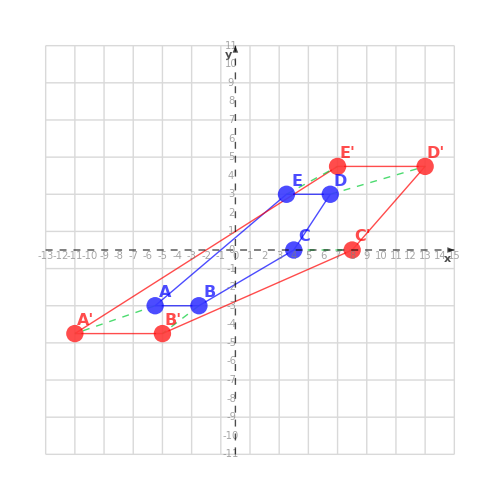

LEGENDA:

• Modré body a čiary: Pôvodný domček

• Červené body a čiary: Transformovaný domček

• Zelené prerušované čiary: Dráha zmeny veľkosti vrcholov

FAREBNÉ OZNAČENIA V MATICOVÝCH VÝPOČTOCH:

• Červená: Transformačná matica

• Modrá: Vstupné súradnice

• Fialová: Medzivýpočty

• Zelená: Výsledné súradnice

Pôvodné vrcholy (modrá):

Vrchol A: {-11/2,-3}

Vrchol B: {-5/2,-3}

Vrchol C: {4,0}

Vrchol D: {13/2,3}

Vrchol E: {7/2,3}

Výsledné vrcholy (červená):

Vrchol A': {-11,-9/2}

Vrchol B': {-5,-9/2}

Vrchol C': {8,0}

Vrchol D': {13,9/2}

Vrchol E': {7,9/2}

Inverzná transformácia:

Pre vrátenie do pôvodného stavu použite koeficienty:

sx' = 1/sx = 1/2 (zmenšovanie v smere osi x)

sy' = 1/sy = 2/3 (zmenšovanie v smere osi y)

MATEMATICKÉ VLASTNOSTI:

• Pri rôznych koeficientoch (sx = 2, sy = 3/2):

- Mení sa tvar (podobnosť) geometrických útvarov

- Uhly medzi úsečkami sa menia

- Pomer dĺžok úsečiek sa mení v závislosti od ich smeru

- Obsah domčeka sa zväčší 3-krát

• Nemení sa poloha počiatku súradnicovej sústavy [0,0]

• Body, ktoré ležia na osi x, zostanú ležať na osi x (ich y-ová súradnica zostáva nulová)

• Body, ktoré ležia na osi y, zostanú ležať na osi y (ich x-ová súradnica zostáva nulová)

POSTUPNÝ VÝPOČET:

Pôvodný domček ABCDE:

Vrcholy:

(-3 | -1
-3 | 2
0 | 4
3 | 2
3 | -1)

Vlastnosti domčeka:

Obsah: 6

Obvod: 19

Po prvej transformácii (Symetria):

Vrcholy domčeka A'B'C'D'E':

(-1 | -3
2 | -3
4 | 0
2 | 3
-1 | 3)

Vlastnosti domčeka:

Obsah: 24

Obvod: 19

Po druhej transformácii (Skosenie):

Vrcholy domčeka A''B''C''D''E'':

(-11/2 | -3
-5/2 | -3
4 | 0
13/2 | 3
7/2 | 3)

Vlastnosti domčeka:

Obsah: 24

Obvod: 28

Po tretej transformácii (Zväčšenie/Zmenšenie):

Vrcholy domčeka A'''B'''C'''D'''E''':

(-11 | -9/2
-5 | -9/2
8 | 0
13 | 9/2
7 | 9/2)

Vlastnosti domčeka:

Obsah: 72

Obvod: 53

VÝPOČET SÚHRNNEJ TRANSFORMAČNEJ MATICE:

Transformačné matice pre jednotlivé transformácie:

Matica pre Symetria (M1):

(0 | 1 | 0
1 | 0 | 0
0 | 0 | 1)

Matica pre Skosenie (M2):

(1 | 3/2 | 0
0 | 1 | 0
0 | 0 | 1)

Matica pre Zväčšenie/Zmenšenie (M3):

(2 | 0 | 0
0 | 3/2 | 0
0 | 0 | 1)

Postupný výpočet súhrnnej matice:

Krok 1: Začíname s maticou prvej transformácie:

M₁ = Matica pre Symetria

(0 | 1 | 0
1 | 0 | 0
0 | 0 | 1)

Krok 2: Násobenie matíc

Pri kompozícii transformácií násobíme matice v opačnom poradí, ako sa aplikujú.

Matica pre aktuálnu transformáciu sa násobí s výsledkom predchádzajúcich transformácií.

M2 · M₁ = Matica pre Skosenie · Matica pre Symetria

Matica pre Skosenie (M2):

(1 | 3/2 | 0
0 | 1 | 0
0 | 0 | 1)

Matica prvej transformácie (M₁):

(0 | 1 | 0
1 | 0 | 0
0 | 0 | 1)

Výpočet násobenia matíc:

C[1,1] = {(1 × 0) + ,(3/2 × 1) + ,(0 × 0)} = 3/2

C[1,2] = {(1 × 1) + ,(3/2 × 0) + ,(0 × 0)} = 1

C[1,3] = {(1 × 0) + ,(3/2 × 0) + ,(0 × 1)} = 0

C[2,1] = {(0 × 0) + ,(1 × 1) + ,(0 × 0)} = 1

C[2,2] = {(0 × 1) + ,(1 × 0) + ,(0 × 0)} = 0

C[2,3] = {(0 × 0) + ,(1 × 0) + ,(0 × 1)} = 0

C[3,1] = {(0 × 0) + ,(0 × 1) + ,(1 × 0)} = 0

C[3,2] = {(0 × 1) + ,(0 × 0) + ,(1 × 0)} = 0

C[3,3] = {(0 × 0) + ,(0 × 0) + ,(1 × 1)} = 1

Výsledok násobenia:

(3/2 | 1 | 0
1 | 0 | 0
0 | 0 | 1)

Krok 3: Násobenie matíc

M3 · (M2 · ... · M₁) = Matica pre Zväčšenie/Zmenšenie · Výsledok predchádzajúcich transformácií (M2 · ... · M₁)

Matica pre Zväčšenie/Zmenšenie (M3):

(2 | 0 | 0
0 | 3/2 | 0
0 | 0 | 1)

Výsledok predchádzajúcich transformácií (M2 · ... · M₁):

(3/2 | 1 | 0
1 | 0 | 0
0 | 0 | 1)

Výpočet násobenia matíc:

C[1,1] = {(2 × 3/2) + ,(0 × 1) + ,(0 × 0)} = 3

C[1,2] = {(2 × 1) + ,(0 × 0) + ,(0 × 0)} = 2

C[1,3] = {(2 × 0) + ,(0 × 0) + ,(0 × 1)} = 0

C[2,1] = {(0 × 3/2) + ,(3/2 × 1) + ,(0 × 0)} = 3/2

C[2,2] = {(0 × 1) + ,(3/2 × 0) + ,(0 × 0)} = 0

C[2,3] = {(0 × 0) + ,(3/2 × 0) + ,(0 × 1)} = 0

C[3,1] = {(0 × 3/2) + ,(0 × 1) + ,(1 × 0)} = 0

C[3,2] = {(0 × 1) + ,(0 × 0) + ,(1 × 0)} = 0

C[3,3] = {(0 × 0) + ,(0 × 0) + ,(1 × 1)} = 1

Výsledok násobenia:

(3 | 2 | 0
3/2 | 0 | 0
0 | 0 | 1)

VÝSLEDNÁ SÚHRNNÁ TRANSFORMAČNÁ MATICA:

(3 | 2 | 0
3/2 | 0 | 0
0 | 0 | 1)

APLIKÁCIA SÚHRNNEJ MATICE NA PÔVODNÝ DOMČEK:

Súhrnná transformačná matica:

(3 | 2 | 0
3/2 | 0 | 0
0 | 0 | 1)

Pôvodný domček ABCDE:

| x | y
A | -3 | -1
B | -3 | 2
C | 0 | 4
D | 3 | 2
E | 3 | -1

Postup pri aplikovaní súhrnnej transformačnej matice na domček:

1. Každý vrchol (x, y) sa rozšíri na homogénne súradnice (x, y, 1)

2. Vynásobí sa súhrnnou transformačnou maticou 3×3

3. Z výsledného vektora vezmeme prvé dve súradnice, čím dostaneme transformovaný vrchol

PODROBNÝ VÝPOČET PRE KAŽDÝ VRCHOL:

Vrchol A:

Pôvodné súradnice: {-3,-1}

V homogénnych súradniciach: {-3,-1,1}

Maticové násobenie:

M · A =

(3 | 2 | 0
3/2 | 0 | 0
0 | 0 | 1) · (-3
-1
1)

Podrobný výpočet:

Riadok 1:

3 · -3 + 2 · -1 + 0 · 1 = -11

Riadok 2:

3/2 · -3 + 0 · -1 + 0 · 1 = -9/2

Riadok 3:

0 · -3 + 0 · -1 + 1 · 1 = 1

Výsledok pre vrchol A:

V homogénnych súradniciach: {-11,-9/2,1}

Transformované súradnice (A'): {-11,-9/2}

Očakávaný výsledok (A'): {-11,-9/2}

✓ Výsledok sa zhoduje s očakávaným bodom.

Vrchol B:

Pôvodné súradnice: {-3,2}

V homogénnych súradniciach: {-3,2,1}

Maticové násobenie:

M · B =

(3 | 2 | 0
3/2 | 0 | 0
0 | 0 | 1) · (-3
2
1)

Podrobný výpočet:

Riadok 1:

3 · -3 + 2 · 2 + 0 · 1 = -5

Riadok 2:

3/2 · -3 + 0 · 2 + 0 · 1 = -9/2

Riadok 3:

0 · -3 + 0 · 2 + 1 · 1 = 1

Výsledok pre vrchol B:

V homogénnych súradniciach: {-5,-9/2,1}

Transformované súradnice (B'): {-5,-9/2}

Očakávaný výsledok (B'): {-5,-9/2}

✓ Výsledok sa zhoduje s očakávaným bodom.

Vrchol C:

Pôvodné súradnice: {0,4}

V homogénnych súradniciach: {0,4,1}

Maticové násobenie:

M · C =

(3 | 2 | 0
3/2 | 0 | 0
0 | 0 | 1) · (0
4
1)

Podrobný výpočet:

Riadok 1:

3 · 0 + 2 · 4 + 0 · 1 = 8

Riadok 2:

3/2 · 0 + 0 · 4 + 0 · 1 = 0

Riadok 3:

0 · 0 + 0 · 4 + 1 · 1 = 1

Výsledok pre vrchol C:

V homogénnych súradniciach: {8,0,1}

Transformované súradnice (C'): {8,0}

Očakávaný výsledok (C'): {8,0}

✓ Výsledok sa zhoduje s očakávaným bodom.

Vrchol D:

Pôvodné súradnice: {3,2}

V homogénnych súradniciach: {3,2,1}

Maticové násobenie:

M · D =

(3 | 2 | 0
3/2 | 0 | 0
0 | 0 | 1) · (3
2
1)

Podrobný výpočet:

Riadok 1:

3 · 3 + 2 · 2 + 0 · 1 = 13

Riadok 2:

3/2 · 3 + 0 · 2 + 0 · 1 = 9/2

Riadok 3:

0 · 3 + 0 · 2 + 1 · 1 = 1

Výsledok pre vrchol D:

V homogénnych súradniciach: {13,9/2,1}

Transformované súradnice (D'): {13,9/2}

Očakávaný výsledok (D'): {13,9/2}

✓ Výsledok sa zhoduje s očakávaným bodom.

Vrchol E:

Pôvodné súradnice: {3,-1}

V homogénnych súradniciach: {3,-1,1}

Maticové násobenie:

M · E =

(3 | 2 | 0
3/2 | 0 | 0
0 | 0 | 1) · (3
-1
1)

Podrobný výpočet:

Riadok 1:

3 · 3 + 2 · -1 + 0 · 1 = 7

Riadok 2:

3/2 · 3 + 0 · -1 + 0 · 1 = 9/2

Riadok 3:

0 · 3 + 0 · -1 + 1 · 1 = 1

Výsledok pre vrchol E:

V homogénnych súradniciach: {7,9/2,1}

Transformované súradnice (E'): {7,9/2}

Očakávaný výsledok (E'): {7,9/2}

✓ Výsledok sa zhoduje s očakávaným bodom.

VÝSLEDNÝ TRANSFORMOVANÝ DOMČEK A'B'C'D'E':

| x | y
A' | -11 | -9/2
B' | -5 | -9/2
C' | 8 | 0
D' | 13 | 9/2
E' | 7 | 9/2

Očakávaný výsledný domček:

| x | y
A' | -11 | -9/2
B' | -5 | -9/2
C' | 8 | 0
D' | 13 | 9/2
E' | 7 | 9/2

✓ OVERENIE ÚSPEŠNÉ: Transformácia pomocou súhrnnej matice dáva správny výsledok.

ZÁVER:

Použitím jedinej transformácie definovanej súhrnnou maticou sme dosiahli rovnaký výsledok,

ako postupným aplikovaním viacerých transformácií. Tento princíp je kľúčový

v počítačovej grafike a umožňuje efektívne vykresľovanie zložitých transformácií.

SÚHRNNÁ VIZUALIZÁCIA:

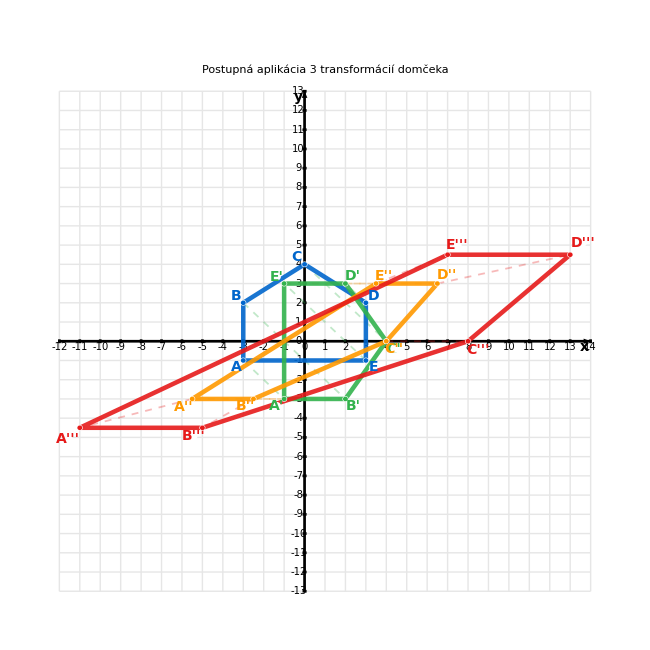

LEGENDA:

• Modré body a čiary: Pôvodný domček ABCDE

• Tmavozelené body a čiary: Domček po prvej transformácii (Symetria)

• Oranžové body a čiary: Domček po druhej transformácii (Skosenie)

• Červené body a čiary: Domček po tretej transformácii (Zväčšenie/Zmenšenie)

Postupnosť transformácií:

1. Symetria podľa priamky y = x

2. Skosenie s parametrami {1.5, 0}

3. Zväčšenie/Zmenšenie s parametrami {2, 1.5}

{{{-3,-1},{-3,2},{0,4},{3,2},{3,-1}},{{{-3,-1},{-3,2},{0,4},{3,2},{3,-1}},{{-1,-3},{2,-3},{4,0},{2,3},{-1,3}},{{-5.5,-3},{-2.5,-3},{4.,0},{6.5,3},{3.5,3}},{{-11.,-4.5},{-5.,-4.5},{8,0.},{13.,4.5},{7.,4.5}},{{-11/2,-3},{-5/2,-3},{4,0},{13/2,3},{7/2,3}}},{Symetria,Skosenie,Zväčšenie/Zmenšenie},Hard,{priamka y=x,{1.5,0},{2,1.5}}}

```mathematica
DomcekTrojitaTransformacia[]
```